# Mass Shooting Analytics

Quantitative Data Visualization

Hannah Garringer, Jun. 29,  2018

Mass shootings in the United States have increased in both quantity and frequency over the past fifty years. While this essay will not attempt to seriously examine possible contributing factors, it will present several descriptive  measures of the available data.

## Preliminary Code

```mathematica
cedata=ResourceData["Mass Shootings in America"];
```

## Demographic Information

There is disagreement among academics as to what constitutes a mass shooting. However, due to limited available data, in this project, mass shooting will be defined as an incident in which there were more than three victims. Important to note here is that when compiling  the database1 used in this project, researchers left out  perpetrators of school shootings if they were tried as minors, as minor status renders much of demographic information unaccessible. This results in a incomplete and skewed data due to the fact that school shooters are disproportionally white and male2.

Below are three charts that describe the gender, race, and age of the mass shooters indicated in the dataset.

This is a pie chart describing the gender of the perpetrators;

```mathematica
PieChart[Counts[cedata[All,"Shooter Sex"]],ChartLegends->{"Male","Female","Male/Female"}]
```

-Graphics-

Below is a pie chart describing the race of the perpetrators;

```mathematica
PieChart[Counts[cedata[All,"Shooter Race"]],ChartLegends->{"White","Black","Unknown","Asian","Asian/Other","Other","Native American","Mixed Race","White/Other","Black/Other"}]
```

-Graphics-

Here is a quantile plot with the ages of the perpetrators;

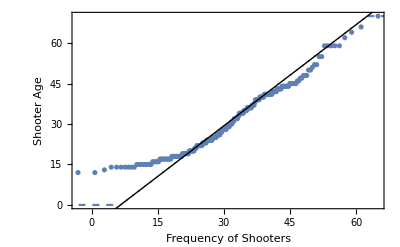

```mathematica
Show[QuantilePlot[Transpose[cedata[All,{"Average Shooter Age"}]]],FrameLabel->{{HoldForm[Shooter Age],None},{HoldForm[Frequency of Shooters],None}}]
```

Finally, below is a formula pulling the median age of the shooters;

```mathematica
centraltendancy=cedata[All,"Average Shooter Age"]//Normal;
Median@Select[centraltendancy,IntegerQ]
```

29

From these charts, it is evident that the vast majority of shooters are male, slightly over half are white, and are mostly between twenty and forty.

## Tracking Mass Shootings

Mass shootings have become more frequent in recent years, but have sharply spiked in the past three years. However, there is a noticeable pattern of shootings peaking every few years.

The below graph shows the frequency of shootings over the past fifty years :

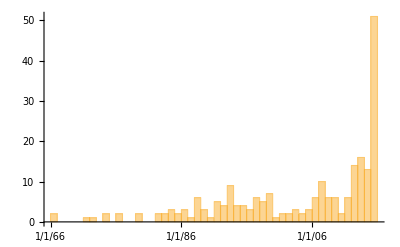

```mathematica
DateHistogram[Transpose[cedata[All,{"Date"}]],"Year"]
```

## Locations Affected

As the below map suggests, mass shootings have, in the past been scattered throughout the states. Perhaps significantly, there are instances where mass shootings are clustered, maybe suggesting that one shooter had been emboldened, or influenced by another.

Below is an animated map, tracking the geographical location of shootings each year up until the present;

```mathematica
ListAnimate[KeyValueMap[GeoListPlot[#2,GeoRange->LinguisticAssistant]&,KeySort[GroupBy[{DateValue[#["Date"],"Year"],#["Position"]}&/@cedata
[All,{"Date","Position"}],First->Last]//Normal]]]
```

## Room for Further Research

There is plenty of room for further research with this data. Specifically of interest would be to used the entity “ZIPCode” and the properties “MedianHouseholdIncome” and “AverageHouseValue” in conjunction with the location data in Out[43] to examine if there is any connection between the class of an area and mass shootings. Additionally, it would be interesting to track if  spikes in mass shootings (seen in Out[42]) coincide with external stressors, tracked through key words or world events in news stories. Finally, tracking the social networks of shooters would likely procure some interesting results.

## Further explorations

Gun Violence

Hegemonic Masculinity

## Author contact information

hannah.r.garringer@gmail.com

## References

1	Wolfram Research, "Mass Shootings in America" from the Wolfram Data Repository. (2015) https://doi.org/10.24097/wolfram.97542.data

2	Newman, Katherine S. 2005. Rampage: Social Roots of School Shootings. Perseus Books, LLC.